```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*INIITIALIZE PARAMETERS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

alpha = 0.5;
beta = 1.0;
delta = 0.5;
katta =5;
qAvg = 1.0;
eta = 0.25;
etaBar = 0.5;
chi = 0.1;
uBar = 1.0;

(*------------------------------------------------------------------------------------------------------------------------------*)
(*AGENTS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*Number of firms*)
n = 10.0;
(*A dummy vector used to identify each firm by a certain number: 1- first firm, 2-second firm,.....n- nth firm*)
Id = Table[i,{i,1,n}];
(*Number of consumers*)
m= 100.0;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PRICING*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*market share of the specialized firm*)
ms[t_,n_,q0_, qi_]:= q0 / Sum[qi[[t,i]],{i,1,n}];
(*markup smart components*)
etaSpec[delta_, etaSpecLag_, msSpec_, etaBar_]:=(1-delta)*etaSpecLag + delta*msSpec*etaBar;
(*price of specialist*)
pSpec[cs_,etaSpec_]:=(1+etaSpec)*cs;
(*price of firm if it produces the smart component*)
pFirmSelf[cSelf_,eta_]:=(1+eta)*cSelf;
(*price of firm if it produces the smart component*)
pFirmSpec[cSpec_,eta_]:=(1+eta)*cSpec;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*MARGINAL COSTS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*Marginal costs of the "usual" component*)
cp = 20.0;
(*Marginal costs of the smart component*)
cs = 10.0;
(*Marginal costs if firm buys smart component from specialist*)
cSelf[cp_, cs_]:=cp + cs
(*Marginal cost if firm buys smart component from specialist*)
cSpec[cp_,cs_, etaSpec_]:=cp + (1+etaSpec)*cs
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PROFIT*)
(*------------------------------------------------------------------------------------------------------------------------------*)
profit[q_,p_,c_]:=q*p - c*q
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*QUALITY*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*quality of specialist*)
(*qualitySpec[t_,uBar_, alpha_, beta_,qSpec_] :=uBar*(1+ beta*qSpec^alpha)*)
(*quality of firm*)
qualityFirm[uBar_, alpha_, beta_,qFirm_ ] :=uBar*(1+ beta*qFirm^alpha)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PROBABILITY*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*A function that computes the probability that consumer j buys from firm i*)
probability[i_,priceList_, qualityList_]:=Module[
{p =priceList, u = qualityList},
Exp[-chi*p[[i]]+ katta*u[[i]]]/Sum[Exp[-chi*p[[k]]+ katta*u[[k]]],{k,1,n}]]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------ EXERCISE 1 a) -------------------------------------------------------------*)
(*---------------------------------(*FIXED STRATEGIES: FIRMS PRODUCE SMART COMPONENT*)------------------------------------*)
```

------------------------------------------------------------------------------------------------------------------------------

Plots of last batch run:

------------------------------------------------------------------------------------------------------------------------------

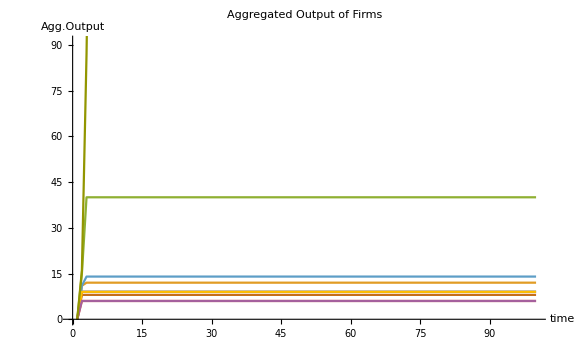

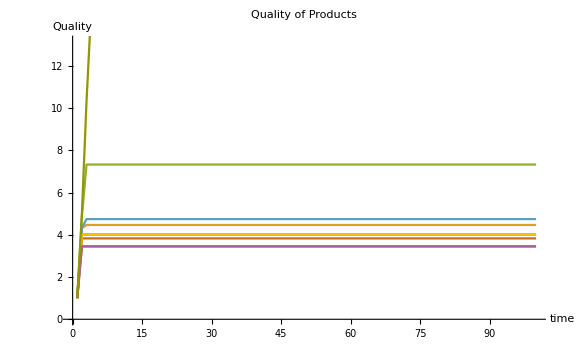

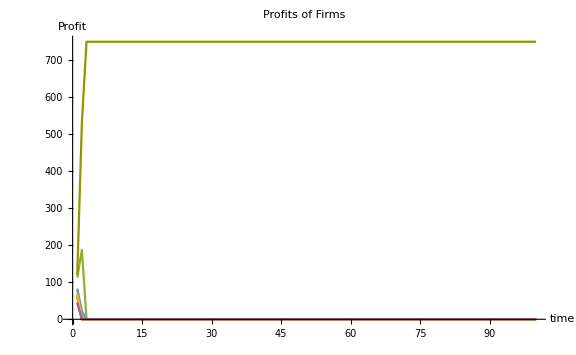

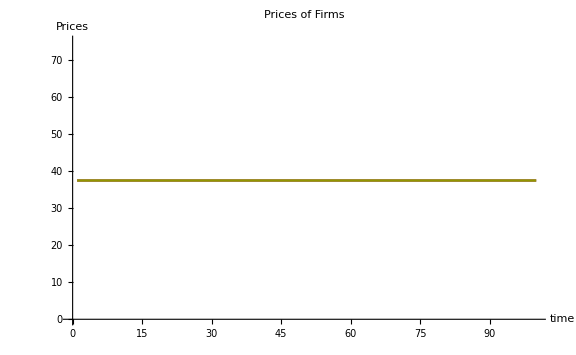

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*Batch Runs*)
(*------------------------------------------------------------------------------------------------------------------------------*)

R=20;
T = 100; (*100*)
count = 0;

Do[
count = count + 1;
(*Store Results in Lists such that 
e.g. priceList[[1,2]] gives the price of the second firm in period 1!!*)

(*prices*)
priceList =Table[Table[0.0,{i,1,n}],{i,1,T}];
qualityList =Table[Table[0.0,{i,1,n}],{i,1,T}];
(*Quantities produced*)
quantPeriod =Table[Table[0.0,{i,1,n}],{i,1,T}];
quantAgg=Table[Table[0.0,{i,1,n}],{i,1,T}]; (*aggregated output*)
(*Profits*)
profitList =Table[Table[0.0,{i,1,n}],{i,1,T}];
(*List of probabilities*)
probList =Table[Table[0.0,{i,1,n}],{i,1,T}];

(*PERIODS*)
Do[
(*compute prices of firms*)
priceList[[t]] =Table[pFirmSelf[cSelf[cp,cs],eta],{i,1,n}];
(*compute aggregated output: depends on aggregate output and period output of LAST PERIOD*)
If[t==1,
quantAgg[[t]]=Table[0.0,{i,1,n}],
quantAgg[[t]]=Table[quantAgg[[t-1,i]]+ quantPeriod[[t-1,i]],{i,1,n}]];
(*compute quality using aggregated output*)
qualityList[[t]] =Table[qualityFirm[uBar, alpha, beta,quantAgg[[t,i]]],{i,1,n}];
(*Compute the probabilities and append them to a list! 
Since each consumer computes these probabilities the same way 
it is necessary to compute them for only one consumer*)
probList[[t]] = Table[probability[i,priceList[[t]], qualityList[[t]]],{i,1,n}];
(*compute demand*)
choiceListAll = RandomChoice[probList[[t]] ->Id,m];
(*Compute quantities produced in period t*)
quantPeriod[[t]] = Table[Count[choiceListAll,i],{i,1,n}];
(*compute profits*)
profitList[[t]] =Table[profit[quantPeriod[[t,i]],priceList[[t,i]],cSelf[cp,cs]],{i,1,n}],

{t,1,T}
];
,{r,1,R}]

(*Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Results of last batch run:"]
Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Period Quantities: ", TableForm[quantPeriod]]
Print["Prices: ",TableForm[priceList]]
Print["Qualities: ",TableForm[qualityList]]
Print["Agg. Quantities: ",TableForm[quantAgg]]
Print["Profits: ",TableForm[profitList]]
Print["Probs: ",TableForm[probList]]*)

Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Plots of last batch run:"]
Print["------------------------------------------------------------------------------------------------------------------------------"]
ListPlot[Table[Table[quantAgg[[t,j]],{t,1,T}],{j,1,n}],Joined->True, ImageSize->Large,PlotLabel->HoldForm[Aggregated Output of Firms],AxesLabel->{HoldForm[time],HoldForm[Agg.Output]}]
ListPlot[Table[Table[qualityList[[t,j]],{t,1,T}],{j,1,n}],Joined->True, ImageSize->Large,PlotLabel->HoldForm[Quality of Products],AxesLabel->{HoldForm[time],HoldForm[Quality]}]
ListPlot[Table[Table[profitList[[t,j]],{t,1,T}],{j,1,n}],Joined->True,PlotRange->All, ImageSize->Large,PlotLabel->HoldForm[Profits of Firms],AxesLabel->{HoldForm[time],HoldForm[Profit]}]
ListPlot[Table[Table[priceList[[t,j]],{t,1,T}],{j,1,n}],Joined->True, ImageSize->Large,PlotLabel->HoldForm[Prices of Firms],AxesLabel->{HoldForm[time],HoldForm[Prices]}]
```

```mathematica
(*count*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------ EXERCISE 1 c) -------------------------------------------------------------*)
(*---------------------------------(*FIXED STRATEGIES: FIRMS BUY SMART COMPONENT*)-----------------------------------------*)
```

------------------------------------------------------------------------------------------------------------------------------

Plots of last batch run:

------------------------------------------------------------------------------------------------------------------------------

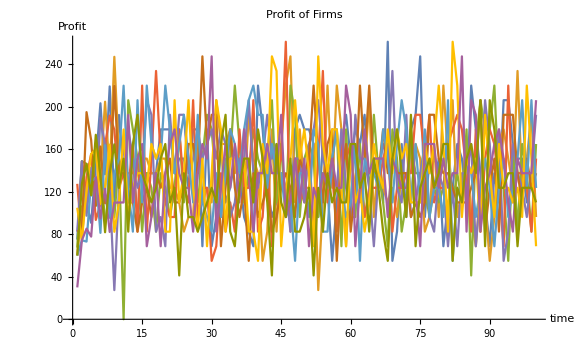

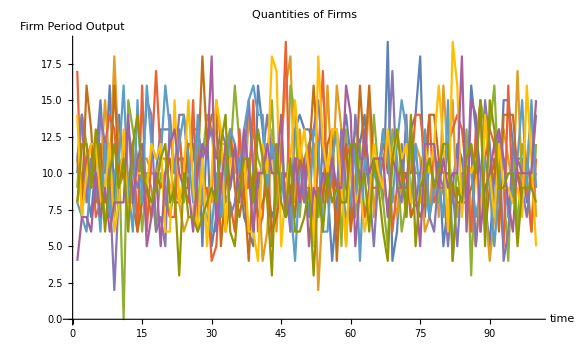

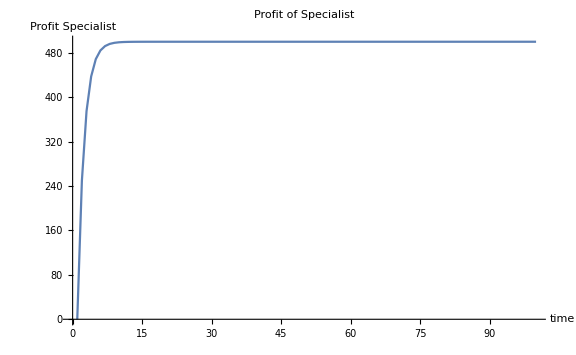

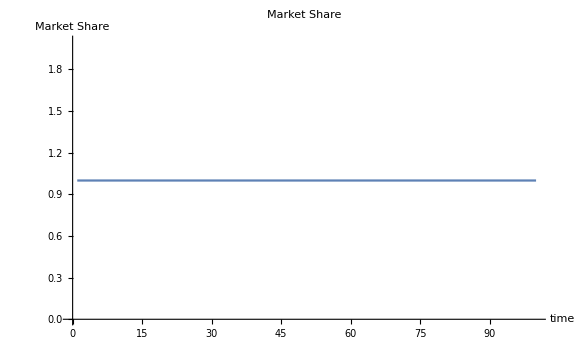

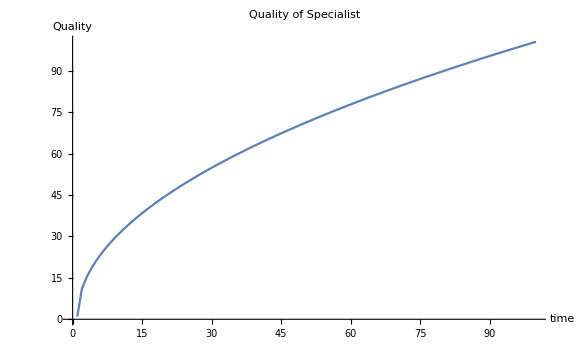

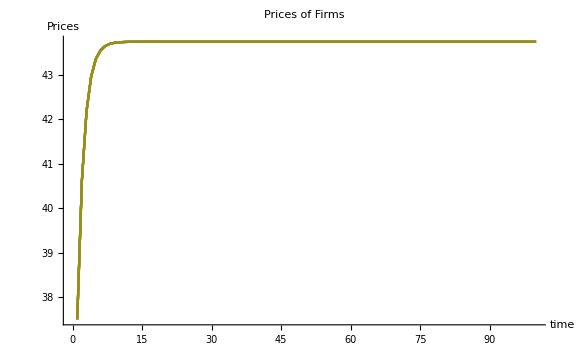

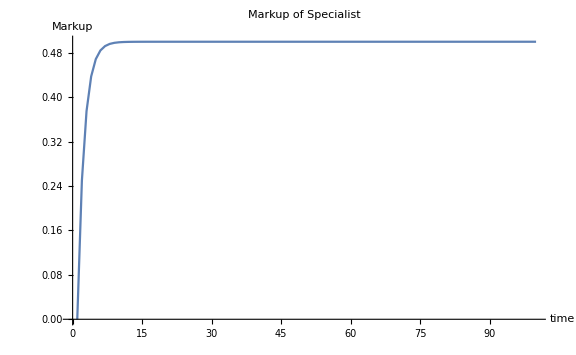

```mathematica
T=100;
R=20;
count=0;
Do[
count=count+1;
(*prices*)
priceSpec =Table[0.0,{i,1,T}];
priceListFirm=Table[Table[0.0,{i,1,n}],{i,1,T}];
(*qualities*)
qualitySpec =Table[0.0,{i,1,T}];
qualityListFirm =Table[Table[0.0,{i,1,n}],{i,1,T}];
(*quantities produced*)
quantPeriodFirm =Table[Table[0.0,{i,1,n}],{i,1,T}];
quantPeriodSpec =Table[0.0,{i,1,T}];
quantAggFirm=Table[Table[0.0,{i,1,n}],{i,1,T}]; (*aggregated output of firm*)
quantAggSpec =Table[0.0,{i,1,T}];(*aggregated output of specialist*)
(*market share of specialist*)
msSpec= Table[0.0,{i,1,T}];
(*markup of specialist*)
markupSpec =Table[0.0,{i,1,T}];
(*profits*)
profitListFirm =Table[Table[0.0,{i,1,n}],{i,1,T}];
profitSpec = Table[0.0,{i,1,T}];
(*list of probabilities*)
probList =Table[Table[0.0,{i,1,n}],{i,1,T}];

(*PERIODS*)
Do[
(*compute markup*)
If[t==1,
markupSpec[[t]]=0.0,
markupSpec[[t]] = etaSpec[delta, markupSpec[[t-1]], msSpec[[t-1]], etaBar];
];
(*compute price of specialist*)
priceSpec[[t]]=pSpec[cs,markupSpec[[t]]];
(*compute prices of firms*)
priceListFirm[[t]] =Table[pFirmSpec[cSpec[cp,cs, markupSpec[[t]]],eta],{i,1,n}];
(*compute aggregated output of specialist: depends on aggregate output and period output of LAST PERIOD*)
If[t==1,
quantAggSpec[[t]]=0.0,
quantAggSpec[[t]]=quantAggSpec[[t-1]]+ quantPeriodSpec[[t-1]]];
(*compute quality using aggregated output*)
qualitySpec[[t]] =uBar*(1+ beta*quantAggSpec[[t]]^alpha);
qualityListFirm[[t]] =Table[qualitySpec[[t]],{i,1,n}];
(*Compute the probabilities and append them to a list! 
Since each consumer computes these probabilities the same way 
it is necessary to compute them for only one consumer*)
probList[[t]] = Table[probability[i,priceListFirm[[t]], qualityListFirm[[t]]],{i,1,n}];
(*compute demand*)
choiceListAll = RandomChoice[probList[[t]] ->Id,m];
(*compute quantities produced by firms in period t*)
quantPeriodFirm[[t]] = Table[Count[choiceListAll,i],{i,1,n}];
(*compute quantities produced by specialist in period t*)
quantPeriodSpec[[t]] =Sum[quantPeriodFirm[[t,i]],{i,1,n}];
(*compute market share*)
msSpec[[t]]=ms[t,n,quantPeriodSpec[[t]], quantPeriodFirm];
(*compute profits*)
profitListFirm[[t]] =Table[profit[quantPeriodFirm[[t,i]],priceListFirm[[t,i]],cSelf[cp,cs]],{i,1,n}];
profitSpec[[t]]=profit[quantPeriodSpec[[t]],priceSpec[[t]],cs],
{t,1,T}
];
,{r,1,R}];

(*Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Results of last batch run:"]
Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Period Quantities: ", TableForm[quantPeriodFirm]]
Print["Prices: ",TableForm[priceListFirm]]
Print["Market Share: ",TableForm[msSpec]]
Print["Profit Firms: ",TableForm[profitListFirm]]
Print["Profit Specialist: ",TableForm[profitSpec]]
Print["Agg. Quantities: ",TableForm[quantAggSpec]]
Print["Quality: ",TableForm[qualityListFirm]]
Print["Probs: ",TableForm[probList]]*)

Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Plots of last batch run:"]
Print["------------------------------------------------------------------------------------------------------------------------------"]
ListPlot[Table[Table[profitListFirm[[t,j]],{t,1,T}],{j,1,n}],Joined->True,PlotRange->All, ImageSize->Large,PlotLabel->HoldForm[Profit of Firms],AxesLabel->{HoldForm[time],HoldForm[Profit]}]
ListPlot[Table[Table[quantPeriodFirm[[t,j]],{t,1,T}],{j,1,n}],Joined->True, ImageSize->Large,PlotLabel->HoldForm[Quantities of Firms],AxesLabel->{HoldForm[time],HoldForm[Firm Period Output]}]
ListPlot[profitSpec,Joined->True, ImageSize->Large,PlotLabel->HoldForm[Profit of Specialist],AxesLabel->{HoldForm[time],HoldForm[Profit Specialist]}]
ListPlot[msSpec,Joined->True, ImageSize->Large,PlotLabel->HoldForm[Market Share],AxesLabel->{HoldForm[time],HoldForm[Market Share]}]
ListPlot[qualitySpec,Joined->True, ImageSize->Large,PlotLabel->HoldForm[Quality of Specialist],AxesLabel->{HoldForm[time],HoldForm[Quality]}]
ListPlot[Table[Table[priceListFirm[[t,j]],{t,1,T}],{j,1,n}],PlotRange->All,Joined->True, ImageSize->Large,PlotLabel->HoldForm[Prices of Firms],AxesLabel->{HoldForm[time],HoldForm[Prices]}]
ListPlot[markupSpec,Joined->True, ImageSize->Large,PlotLabel->HoldForm[Markup of Specialist],AxesLabel->{HoldForm[time],HoldForm[Markup]}]
```